```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

FreeEnergyAvg[gpo_,inputtemplates_,EnergyMatrix_] := Mean[FreeEnergy[gpo,EnergyMatrix,#] &/@ inputtemplates];

(*Specifically, this is the equilibrium per monomer free energy*)
FreeEnergy[gpo_,EnergyMatrix_,Template_] := Module[{len,last,FreeEnergyTot},
		len = Length[Template];	

		last = Last[Template];
		FreeEnergyTot = Log[ Exp[EnergyMatrix[[1,last]]] 
			+ Exp[EnergyMatrix[[2,last]]]] ;
		
		Return[FreeEnergyTot];
	]
```

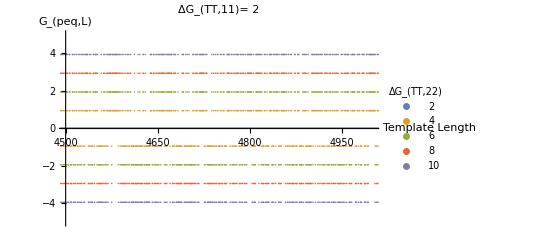

```mathematica
copysize= 2;
templatesize = 2;

Get["masterTemplate"];
inputtemplate = masterTemplate;

KineticMatrix = {{0.0,0.0},{0.0,0.0}};
FEData = {};

domainLengths = Range[2,10000];
Domain = masterTemplate[[1;;#]] &/@ domainLengths;

For [ x = 2.0,x<10.1,x = x+2.0,
	EnergyMatrix =  {{2.0,0},{0,x}};
	
	MeanFE =FreeEnergy[-Log[2],EnergyMatrix,#]  &/@ Domain;
	MeanFE = MeanFE - (Log[E^2+1]+Log[E^x+1])/2;
	FEData =Append[FEData,Transpose@{domainLengths,MeanFE}];
]

mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[FEData,AxesLabel->{"Template Length",Subscript["G","peq,L"]},
		PlotLegends->Placed[pl,Right], PlotRange -> {{4500,5000},{-5,5}},PlotLabel->Row[{Subscript["ΔG","TT,11"],"= 2"}]]
```

```mathematica
Save["TempTherm.FreeEnergy",FEData]
```

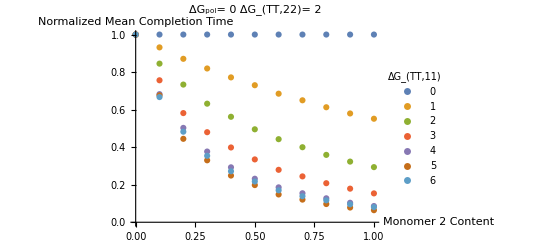

```mathematica
KineticMatrix =  {{0,0},{0,0}};
gpo = 0.0;

PreDomain =  Range[0,1,0.1];
ErrorData= {};
Raw = {};
Domain = {1-#,#} &/@PreDomain;

For [ x = 0.0,x<=6.1,x = x+1.0,
	EnergyMatrix =  {{6.0,x},{0,6.0}};
	MeanErrors =RandomMarkovTime[  2,#,10000,gpo,EnergyMatrix,KineticMatrix] &/@Domain;
	times = MeanErrors/Max[MeanErrors[[1]],Last[MeanErrors]];
	ErrorData =Append[ErrorData,Transpose@{PreDomain,times}];
	Raw =Append[Raw,Transpose@{PreDomain,MeanErrors}];
]

mu={0,1,2,3,4,5,6};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,11"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[ErrorData,AxesLabel->{"Monomer 2 Content","Normalized Mean Completion Time"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","pol"],"= 0    ",
		Subscript["ΔG","TT,22"],"= 2"}]]
```

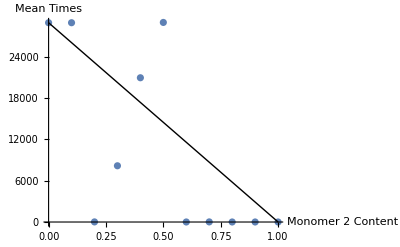

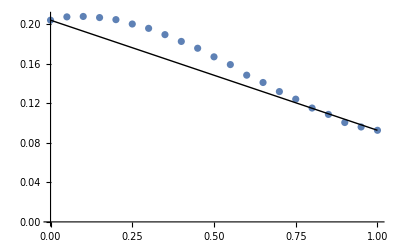

```mathematica
data1 = Raw[[6]];
p1 =ListPlot[data1,AxesLabel->{"Monomer 2 Content","Mean Times"}];
p2 = Graphics[Line[{data1[[1]],data1[[-1]]}]];
Show[{p1,p2}]
```

```mathematica
Save["Normalized",ErrorData]
Save["Unnormalized",Raw]
```

```mathematica
Max[1,2]
```

2

```mathematica
FEData[[3]]
```

{{1,1.68475},{2,0.5145},{3,0.105618},{4,-0.0971736},{5,-0.217528},{6,-0.295965},{7,-0.352219},{8,-0.395835},{9,-0.428203},{10,-0.452798},{20,-0.573612},{30,-0.613164},{40,-0.63369},{50,-0.645297},{60,-0.653516},{70,-0.659166},{80,-0.663286},{90,-0.666566},{100,-0.669382}}

```mathematica
A =RandomMarkovTime[  2,#,10000,gpo,{{2,0},{0,10}},{{0,0},{0,0}}] &/@Domain
```

{18.3189,1.06041×10^6,4.26102×10^6,9.16401×10^6,1.65808×10^7,2.39577×10^7,3.1183×10^7,3.85206×10^7,4.30053×10^7,4.06778×10^7,5.46657×10^6}

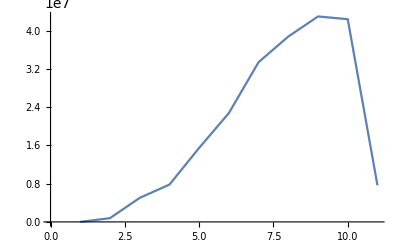

```mathematica
ListLinePlot[{18.35395563888888,783779.0198124667,5.0257612626797715*^6,7.7980114449028615*^6,1.5479817935539082*^7,2.276936415142884*^7,3.342045807227078*^7,3.877920194749455*^7,4.2983133707566366*^7,4.2411030454278715*^7,7.659289304499788*^6}]
```

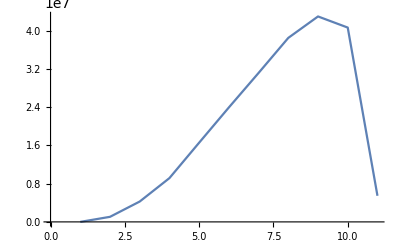

```mathematica
ListLinePlot[A]
```

```mathematica
FEData
```

$Aborted

```mathematica
MeanVel
```

MeanVel

```mathematica
FreeEnergy[-Log[2],EnergyMatrix,{2,2}]
```

0

```mathematica
FreeEnergyAvg[-Log[2],Domain[[2]],{{2.0,0.0},{0.0,6.0}}]
```

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

Last::normal: Nonatomic expression expected at position 1 in Last[Domain].

Part::pkspec1: The expression Last[Domain] cannot be used as a part specification.

Power::infy: Infinite expression 1/0 encountered.

Last::normal: Nonatomic expression expected at position 1 in Last[2].

Part::pkspec1: The expression Last[2] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Mean[ComplexInfinity⟦ComplexInfinity⟧]

```mathematica
last = 2
Log[ Exp[EnergyMatrix[[1,last]]] + Exp[EnergyMatrix[[2,last]]]]
```

2

10.

```mathematica
Domain[[3]]
FreeEnergy[-Log[2],EnergyMatrix,Domain[[3]]]
```

{2,2,2,1}

2.12693

```mathematica
MeanFE
```

{10.,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.,10.,10.,10.,10.,10.,10.,10.,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,2.12693,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,10.,10.,10.,2.12693,10.,2.12693,10.,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,10.,2.12693,10.,10.,10.,10.,10.,2.12693,2.12693,10.,10.,10.,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,2.12693,10.,10.,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,10.,10.,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,2.12693,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,10.,10.,10.,10.,2.12693,2.12693,10.,10.,10.,10.,10.,10.,10.,10.,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,10.,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,10.,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,10.,10.,10.,10.,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,10.,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,10.,10.,2.12693,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,10.,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,10.,10.,2.12693,10.,10.,10.,10.,10.,10.,10.,10.,10.,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,10.,2.12693,10.,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,10.,10.,2.12693,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,10.,2.12693,2.12693,10.,2.12693,10.,10.,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,10.,10.,10.,10.,10.,10.,10.,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,10.,10.,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,2.12693,10.,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,2.12693,10.,10.,10.,2.12693,10.,10.,10.,10.,2.12693,10.,2.12693,10.,10.,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,2.12693,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,10.,10.,10.,2.12693,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,2.12693,10.,2.12693,10.,10.,2.12693,10.,10.,10.,10.,2.12693,10.,10.,2.12693,2.12693,2.12693,10.,10.,2.12693,10.,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,2.12693,10.,2.12693,10.,2.12693,10.,10.,2.12693,2.12693,10.,10.,10.,2.12693,2.12693,10.,2.12693,2.12693,2.12693,10.,2.12693,10.,2.12693,10.,10.}

```mathematica
FEData[[5]]
```

{{2,10.},{3,10.},{4,2.12693},{5,10.},{6,2.12693},{7,2.12693},{8,2.12693},{9,2.12693},{10,10.},{11,2.12693},{12,10.},{13,2.12693},{14,2.12693},{15,2.12693},{16,10.},{17,2.12693},{18,2.12693},{19,2.12693},{20,10.},{21,10.},{22,10.},{23,10.},{24,2.12693},{25,2.12693},{26,10.},{27,2.12693},{28,10.},{29,10.},{30,2.12693},{31,2.12693},{32,2.12693},{33,10.},{34,2.12693},{35,10.},{36,2.12693},{37,2.12693},{38,2.12693},{39,2.12693},{40,10.},{41,10.},{42,2.12693},{43,10.},{44,10.},{45,2.12693},{46,10.},{47,10.},{48,10.},{49,10.},{50,10.},{51,2.12693},{52,2.12693},{53,10.},{54,2.12693},{55,10.},{56,2.12693},{57,10.},{58,10.},{59,10.},{60,10.},{61,10.},{62,10.},{63,10.},{64,10.},{65,10.},{66,2.12693},{67,10.},{68,2.12693},{69,10.},{70,10.},{71,10.},{72,10.},{73,2.12693},{74,10.},{75,10.},{76,10.},{77,10.},{78,2.12693},{79,2.12693},{80,10.},{81,2.12693},{82,2.12693},{83,10.},{84,2.12693},{85,2.12693},{86,2.12693},{87,10.},{88,10.},{89,2.12693},{90,10.},{91,10.},{92,2.12693},{93,10.},{94,2.12693},{95,10.},{96,2.12693},{97,10.},{98,10.},{99,2.12693},{100,2.12693},{101,2.12693},{102,10.},{103,2.12693},{104,2.12693},{105,10.},{106,10.},{107,2.12693},{108,10.},{109,2.12693},{110,2.12693},{111,10.},{112,2.12693},{113,2.12693},{114,10.},{115,2.12693},{116,10.},{117,2.12693},{118,2.12693},{119,10.},{120,2.12693},{121,2.12693},{122,2.12693},{123,10.},{124,10.},{125,10.},{126,10.},{127,10.},{128,2.12693},{129,2.12693},{130,2.12693},{131,2.12693},{132,2.12693},{133,2.12693},{134,2.12693},{135,10.},{136,10.},{137,2.12693},{138,10.},{139,2.12693},{140,10.},{141,10.},{142,10.},{143,2.12693},{144,2.12693},{145,2.12693},{146,2.12693},{147,10.},{148,10.},{149,2.12693},{150,10.},{151,2.12693},{152,2.12693},{153,10.},{154,10.},{155,10.},{156,2.12693},{157,10.},{158,2.12693},{159,10.},{160,2.12693},{161,10.},{162,2.12693},{163,10.},{164,2.12693},{165,2.12693},{166,10.},{167,2.12693},{168,2.12693},{169,10.},{170,10.},{171,2.12693},{172,2.12693},{173,10.},{174,2.12693},{175,10.},{176,2.12693},{177,2.12693},{178,2.12693},{179,10.},{180,2.12693},{181,2.12693},{182,2.12693},{183,10.},{184,2.12693},{185,2.12693},{186,2.12693},{187,2.12693},{188,10.},{189,2.12693},{190,10.},{191,2.12693},{192,2.12693},{193,2.12693},{194,2.12693},{195,10.},{196,10.},{197,2.12693},{198,10.},{199,10.},{200,10.},{201,2.12693},{202,10.},{203,10.},{204,2.12693},{205,2.12693},{206,10.},{207,2.12693},{208,10.},{209,2.12693},{210,2.12693},{211,10.},{212,2.12693},{213,10.},{214,10.},{215,2.12693},{216,10.},{217,2.12693},{218,2.12693},{219,2.12693},{220,10.},{221,2.12693},{222,2.12693},{223,2.12693},{224,2.12693},{225,10.},{226,10.},{227,2.12693},{228,2.12693},{229,10.},{230,2.12693},{231,10.},{232,10.},{233,2.12693},{234,10.},{235,10.},{236,2.12693},{237,10.},{238,10.},{239,10.},{240,10.},{241,10.},{242,2.12693},{243,10.},{244,10.},{245,10.},{246,10.},{247,10.},{248,2.12693},{249,2.12693},{250,10.},{251,10.},{252,10.},{253,2.12693},{254,10.},{255,2.12693},{256,10.},{257,10.},{258,2.12693},{259,10.},{260,10.},{261,2.12693},{262,10.},{263,2.12693},{264,10.},{265,10.},{266,2.12693},{267,10.},{268,2.12693},{269,10.},{270,2.12693},{271,2.12693},{272,2.12693},{273,2.12693},{274,2.12693},{275,10.},{276,2.12693},{277,2.12693},{278,2.12693},{279,2.12693},{280,2.12693},{281,2.12693},{282,10.},{283,10.},{284,10.},{285,10.},{286,2.12693},{287,10.},{288,2.12693},{289,10.},{290,2.12693},{291,2.12693},{292,10.},{293,2.12693},{294,2.12693},{295,2.12693},{296,2.12693},{297,2.12693},{298,10.},{299,2.12693},{300,10.},{301,10.},{302,2.12693},{303,10.},{304,10.},{305,10.},{306,10.},{307,10.},{308,2.12693},{309,10.},{310,10.},{311,10.},{312,10.},{313,2.12693},{314,2.12693},{315,2.12693},{316,2.12693},{317,10.},{318,2.12693},{319,10.},{320,10.},{321,10.},{322,10.},{323,2.12693},{324,10.},{325,2.12693},{326,10.},{327,10.},{328,10.},{329,10.},{330,10.},{331,10.},{332,2.12693},{333,2.12693},{334,2.12693},{335,2.12693},{336,2.12693},{337,10.},{338,10.},{339,10.},{340,2.12693},{341,10.},{342,2.12693},{343,10.},{344,10.},{345,2.12693},{346,2.12693},{347,2.12693},{348,2.12693},{349,10.},{350,2.12693},{351,2.12693},{352,10.},{353,10.},{354,10.},{355,2.12693},{356,2.12693},{357,10.},{358,2.12693},{359,10.},{360,10.},{361,10.},{362,10.},{363,2.12693},{364,2.12693},{365,10.},{366,2.12693},{367,10.},{368,2.12693},{369,10.},{370,2.12693},{371,10.},{372,2.12693},{373,2.12693},{374,10.},{375,10.},{376,10.},{377,10.},{378,10.},{379,2.12693},{380,2.12693},{381,10.},{382,10.},{383,10.},{384,10.},{385,10.},{386,10.},{387,10.},{388,10.},{389,2.12693},{390,10.},{391,2.12693},{392,10.},{393,10.},{394,10.},{395,10.},{396,2.12693},{397,2.12693},{398,2.12693},{399,2.12693},{400,2.12693},{401,10.},{402,10.},{403,10.},{404,10.},{405,2.12693},{406,2.12693},{407,2.12693},{408,2.12693},{409,2.12693},{410,2.12693},{411,10.},{412,2.12693},{413,10.},{414,10.},{415,10.},{416,10.},{417,2.12693},{418,10.},{419,2.12693},{420,2.12693},{421,2.12693},{422,2.12693},{423,10.},{424,10.},{425,10.},{426,10.},{427,10.},{428,2.12693},{429,10.},{430,2.12693},{431,2.12693},{432,10.},{433,10.},{434,2.12693},{435,10.},{436,10.},{437,2.12693},{438,10.},{439,10.},{440,10.},{441,2.12693},{442,10.},{443,2.12693},{444,2.12693},{445,2.12693},{446,2.12693},{447,10.},{448,10.},{449,2.12693},{450,2.12693},{451,10.},{452,2.12693},{453,2.12693},{454,2.12693},{455,2.12693},{456,10.},{457,2.12693},{458,2.12693},{459,2.12693},{460,10.},{461,10.},{462,2.12693},{463,10.},{464,2.12693},{465,10.},{466,10.},{467,10.},{468,10.},{469,10.},{470,10.},{471,10.},{472,10.},{473,2.12693},{474,2.12693},{475,2.12693},{476,2.12693},{477,10.},{478,2.12693},{479,10.},{480,2.12693},{481,2.12693},{482,2.12693},{483,10.},{484,10.},{485,2.12693},{486,10.},{487,2.12693},{488,2.12693},{489,10.},{490,10.},{491,2.12693},{492,2.12693},{493,10.},{494,10.},{495,2.12693},{496,10.},{497,10.},{498,10.},{499,10.},{500,2.12693},{501,2.12693},{502,10.},{503,10.},{504,2.12693},{505,10.},{506,2.12693},{507,2.12693},{508,10.},{509,10.},{510,10.},{511,2.12693},{512,2.12693},{513,2.12693},{514,10.},{515,2.12693},{516,10.},{517,2.12693},{518,10.},{519,10.},{520,2.12693},{521,10.},{522,10.},{523,10.},{524,10.},{525,2.12693},{526,2.12693},{527,2.12693},{528,2.12693},{529,2.12693},{530,2.12693},{531,10.},{532,2.12693},{533,2.12693},{534,2.12693},{535,2.12693},{536,10.},{537,10.},{538,10.},{539,10.},{540,2.12693},{541,2.12693},{542,2.12693},{543,2.12693},{544,10.},{545,10.},{546,2.12693},{547,10.},{548,10.},{549,2.12693},{550,10.},{551,2.12693},{552,2.12693},{553,10.},{554,2.12693},{555,2.12693},{556,2.12693},{557,2.12693},{558,10.},{559,2.12693},{560,2.12693},{561,2.12693},{562,2.12693},{563,2.12693},{564,10.},{565,10.},{566,2.12693},{567,2.12693},{568,10.},{569,10.},{570,2.12693},{571,2.12693},{572,2.12693},{573,10.},{574,10.},{575,10.},{576,2.12693},{577,10.},{578,10.},{579,10.},{580,2.12693},{581,2.12693},{582,10.},{583,2.12693},{584,10.},{585,10.},{586,2.12693},{587,10.},{588,2.12693},{589,2.12693},{590,2.12693},{591,2.12693},{592,2.12693},{593,10.},{594,2.12693},{595,2.12693},{596,2.12693},{597,2.12693},{598,10.},{599,2.12693},{600,10.},{601,10.},{602,10.},{603,10.},{604,10.},{605,10.},{606,2.12693},{607,10.},{608,10.},{609,2.12693},{610,2.12693},{611,10.},{612,10.},{613,10.},{614,10.},{615,2.12693},{616,10.},{617,10.},{618,10.},{619,10.},{620,10.},{621,10.},{622,10.},{623,10.},{624,10.},{625,2.12693},{626,10.},{627,10.},{628,10.},{629,10.},{630,2.12693},{631,10.},{632,2.12693},{633,10.},{634,2.12693},{635,2.12693},{636,10.},{637,2.12693},{638,2.12693},{639,2.12693},{640,10.},{641,2.12693},{642,10.},{643,2.12693},{644,10.},{645,10.},{646,10.},{647,10.},{648,2.12693},{649,10.},{650,10.},{651,2.12693},{652,2.12693},{653,10.},{654,10.},{655,2.12693},{656,2.12693},{657,2.12693},{658,2.12693},{659,2.12693},{660,10.},{661,2.12693},{662,10.},{663,10.},{664,10.},{665,10.},{666,2.12693},{667,2.12693},{668,2.12693},{669,2.12693},{670,10.},{671,2.12693},{672,2.12693},{673,2.12693},{674,10.},{675,10.},{676,10.},{677,2.12693},{678,10.},{679,10.},{680,10.},{681,10.},{682,2.12693},{683,10.},{684,10.},{685,2.12693},{686,2.12693},{687,2.12693},{688,2.12693},{689,2.12693},{690,10.},{691,10.},{692,10.},{693,10.},{694,10.},{695,10.},{696,2.12693},{697,2.12693},{698,10.},{699,10.},{700,10.},{701,10.},{702,2.12693},{703,10.},{704,2.12693},{705,2.12693},{706,10.},{707,2.12693},{708,10.},{709,2.12693},{710,10.},{711,10.},{712,2.12693},{713,10.},{714,10.},{715,10.},{716,2.12693},{717,2.12693},{718,10.},{719,2.12693},{720,10.},{721,10.},{722,10.},{723,2.12693},{724,10.},{725,2.12693},{726,2.12693},{727,10.},{728,2.12693},{729,10.},{730,2.12693},{731,10.},{732,10.},{733,2.12693},{734,2.12693},{735,10.},{736,10.},{737,2.12693},{738,2.12693},{739,10.},{740,10.},{741,10.},{742,10.},{743,10.},{744,10.},{745,10.},{746,10.},{747,10.},{748,2.12693},{749,2.12693},{750,2.12693},{751,10.},{752,10.},{753,2.12693},{754,2.12693},{755,2.12693},{756,2.12693},{757,10.},{758,2.12693},{759,2.12693},{760,10.},{761,10.},{762,2.12693},{763,2.12693},{764,2.12693},{765,10.},{766,2.12693},{767,2.12693},{768,10.},{769,2.12693},{770,10.},{771,10.},{772,2.12693},{773,10.},{774,10.},{775,10.},{776,10.},{777,10.},{778,10.},{779,2.12693},{780,10.},{781,2.12693},{782,2.12693},{783,10.},{784,10.},{785,2.12693},{786,10.},{787,10.},{788,2.12693},{789,10.},{790,2.12693},{791,10.},{792,10.},{793,10.},{794,10.},{795,2.12693},{796,10.},{797,10.},{798,2.12693},{799,2.12693},{800,10.},{801,10.},{802,2.12693},{803,2.12693},{804,10.},{805,2.12693},{806,2.12693},{807,10.},{808,2.12693},{809,10.},{810,10.},{811,10.},{812,2.12693},{813,10.},{814,10.},{815,10.},{816,10.},{817,2.12693},{818,10.},{819,2.12693},{820,10.},{821,10.},{822,10.},{823,2.12693},{824,2.12693},{825,10.},{826,2.12693},{827,2.12693},{828,2.12693},{829,10.},{830,2.12693},{831,10.},{832,2.12693},{833,2.12693},{834,2.12693},{835,2.12693},{836,10.},{837,10.},{838,10.},{839,2.12693},{840,10.},{841,2.12693},{842,2.12693},{843,2.12693},{844,10.},{845,2.12693},{846,10.},{847,2.12693},{848,2.12693},{849,10.},{850,2.12693},{851,2.12693},{852,10.},{853,10.},{854,2.12693},{855,2.12693},{856,2.12693},{857,10.},{858,2.12693},{859,2.12693},{860,2.12693},{861,2.12693},{862,2.12693},{863,10.},{864,10.},{865,10.},{866,10.},{867,2.12693},{868,2.12693},{869,2.12693},{870,2.12693},{871,10.},{872,10.},{873,10.},{874,10.},{875,2.12693},{876,2.12693},{877,2.12693},{878,2.12693},{879,10.},{880,10.},{881,2.12693},{882,2.12693},{883,2.12693},{884,2.12693},{885,10.},{886,10.},{887,2.12693},{888,2.12693},{889,2.12693},{890,2.12693},{891,2.12693},{892,10.},{893,10.},{894,2.12693},{895,2.12693},{896,2.12693},{897,10.},{898,2.12693},{899,2.12693},{900,10.},{901,2.12693},{902,2.12693},{903,10.},{904,10.},{905,2.12693},{906,2.12693},{907,2.12693},{908,2.12693},{909,2.12693},{910,10.},{911,2.12693},{912,2.12693},{913,2.12693},{914,10.},{915,10.},{916,2.12693},{917,2.12693},{918,2.12693},{919,2.12693},{920,2.12693},{921,2.12693},{922,10.},{923,2.12693},{924,10.},{925,2.12693},{926,2.12693},{927,10.},{928,10.},{929,2.12693},{930,2.12693},{931,10.},{932,10.},{933,10.},{934,10.},{935,2.12693},{936,2.12693},{937,10.},{938,10.},{939,2.12693},{940,2.12693},{941,10.},{942,10.},{943,2.12693},{944,10.},{945,10.},{946,2.12693},{947,2.12693},{948,2.12693},{949,2.12693},{950,10.},{951,2.12693},{952,10.},{953,10.},{954,2.12693},{955,10.},{956,10.},{957,10.},{958,10.},{959,2.12693},{960,10.},{961,10.},{962,2.12693},{963,2.12693},{964,2.12693},{965,10.},{966,10.},{967,2.12693},{968,10.},{969,10.},{970,2.12693},{971,10.},{972,10.},{973,2.12693},{974,2.12693},{975,10.},{976,10.},{977,2.12693},{978,10.},{979,2.12693},{980,10.},{981,2.12693},{982,10.},{983,10.},{984,2.12693},{985,2.12693},{986,10.},{987,10.},{988,10.},{989,2.12693},{990,2.12693},{991,10.},{992,2.12693},{993,2.12693},{994,2.12693},{995,10.},{996,2.12693},{997,10.},{998,2.12693},{999,10.},{1000,10.}}

```mathematica
FEData[[5]]
```

```mathematica
0.5*Log[E^2]+0.5*Log[E^10]
```

6.